```mathematica
plotOffGasFileCO2[svnPath_,strainPath_]:= 
With[{matrixCO2=Import[svnPath<>"/Chemostat analysis/chemostatAnalysis/data/"<>strainPath<>"/offGas.csv"]},DateListPlot[
Transpose[{matrixCO2[[2;;All,1]],matrixCO2[[2;;All,2]]}],PlotLegends->"CO_2%"]
]
plotOffGasFileEtOH[svnPath_,strainPath_]:= 
With[{matrixEtOH=Import[svnPath<>"/Chemostat analysis/chemostatAnalysis/data/"<>strainPath<>"/offGas.csv"]},DateListPlot[
Transpose[{matrixEtOH[[2;;All,1]],matrixEtOH[[2;;All,4]]}],PlotLegends->"EtOH [ppm]"]
]
plotOffGasFileO2[svnPath_,strainPath_]:= 
With[{matrixO2=Import[svnPath<>"/Chemostat analysis/chemostatAnalysis/data/"<>strainPath<>"/offGas.csv"]},DateListPlot[
Transpose[{matrixO2[[2;;All,1]],matrixO2[[2;;All,5]]}],PlotLegends->"O_2%"]
]
```

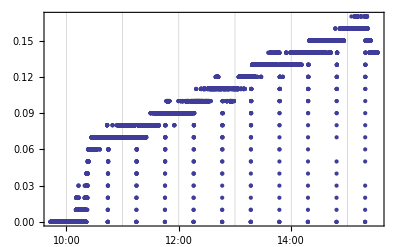

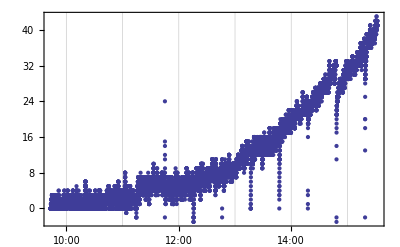

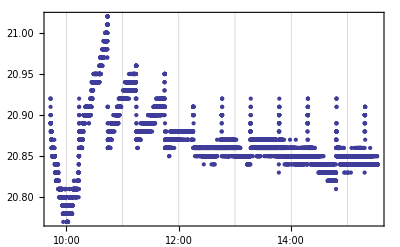

```mathematica
svnPath ="~/Dropbox/School/mblab";
strainPath = "YMR037C/05.29.14/chem4";
plotOffGasFileCO2[svnPath,strainPath]
plotOffGasFileEtOH[svnPath,strainPath]
plotOffGasFileO2[svnPath,strainPath]
Clear[strainPath];
```

```mathematica
plotOffGasAll[svnPath_,strainPath_] :=
With[{matrix=Import[svnPath<>"/Chemostat analysis/chemostatAnalysis/data/"<>strainPath<>"/offGas.csv"]},
{DateListPlot[
Transpose[{matrix[[2;;All,1]],matrix[[2;;All,2]]}],PlotLegends->"CO_2%"],DateListPlot[
Transpose[{matrix[[2;;All,1]],matrix[[2;;All,4]]}],PlotLegends->"EtOH [ppm]"],DateListPlot[
Transpose[{matrix[[2;;All,1]],matrix[[2;;All,5]]}],PlotLegends->"O_2%"
]
}
]
```

```mathematica
svnPath ="~/Dropbox/School/mblab";
strainPath = "YMR037C/05.29.14/chem4";
plotOffGasAll[svnPath,strainPath]
Clear[strainPath];
```

{-Graphics-,-Graphics-,-Graphics-}